This notebook is to study the effect of J on stacking energy models.

```mathematica
Jstacking=Table[u/.FindRoot[ⅇ^(-J×x)×∑_(l=1)^10000 ⅇ^(-u×l)-1,{u,-0.001}],{J,0.5,5,0.5},{x,0.01,15,0.1}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{0.69065,0.666025,0.642025,0.618647,0.595891,0.573753,0.552231,0.531318,0.511012,0.491305,0.472192,0.453666,0.435719,0.418343,0.40153,0.38527,0.369553,0.354371,0.339711,0.325564,0.311919,0.298765,0.286089,0.27388,0.262127,0.250818,0.23994,0.229481,0.21943,0.209775,0.200503,0.191603,0.183063,0.174871,0.167015,0.159485,0.15227,0.145358,0.138738,0.1324,0.126333,0.120528,0.114975,0.109664,0.104586,0.0997309,0.0950909,0.0906571,0.0864212,0.0823752,0.0785113,0.0748219,0.0712998,0.0679379,0.0647294,0.0616679,0.0587469,0.0559604,0.0533026,0.0507679,0.0483508,0.0460461,0.0438489,0.0417544,0.039758,0.0378552,0.0360418,0.0343139,0.0326674,0.0310987,0.0296042,0.0281805,0.0268244,0.0255327,0.0243025,0.0231309,0.0220151,0.0209526,0.0199408,0.0189775,0.0180602,0.0171869,0.0163555,0.015564,0.0148106,0.0140933,0.0134106,0.0127607,0.0121421,0.0115533,0.0109929,0.0104596,0.00995202,0.00946894,0.00900921,0.0085717,0.00815536,0.00775915,0.00738213,0.00702336,0.00668197,0.00635712,0.00604801,0.00575389,0.00547404,0.00520776,0.0049544,0.00471334,0.00448399,0.00426577,0.00405814,0.00386061,0.00367267,0.00349386,0.00332375,0.0031619,0.00300793,0.00286144,0.00272207,0.00258949,0.00246335,0.00234335,0.00222919,0.00212059,0.00201727,0.00191898,0.00182548,0.00173653,0.0016519,0.0015714,0.00149482,0.00142197,0.00135267,0.00128674,0.00122402,0.00116435,0.00110759,0.00105359,0.00100221,0.00095333,0.000906818,0.000862556,0.000820429,0.000780326,0.000742142,0.000705775,0.000671126,0.000638101,0.000606609,0.000576563},{0.68816,0.639659,0.59365,0.550112,0.509014,0.470313,0.433956,0.399879,0.368011,0.338274,0.310582,0.284847,0.260977,0.238875,0.218447,0.199596,0.182228,0.166248,0.151565,0.138091,0.125741,0.114433,0.10409,0.0946384,0.0860082,0.0781346,0.0709565,0.0644168,0.0584623,0.0530437,0.0481153,0.043635,0.0395636,0.0358653,0.0325071,0.0294587,0.0266924,0.0241827,0.0219065,0.0198423,0.0179709,0.0162746,0.0147372,0.0133441,0.0120819,0.0109384,0.00990263,0.00896448,0.00811485,0.00734544,0.00664875,0.00601794,0.00544681,0.00492976,0.00446167,0.00403794,0.00365438,0.0033072,0.00299295,0.00270852,0.00245108,0.00221809,0.00200722,0.00181638,0.00164367,0.00148737,0.00134592,0.00121792,0.00110207,0.000997214,0.000902293,0.000816329,0.000738425,0.000667752,0.000603541,0.000545082,0.000491724,0.000442875,0.000397999,0.000356617,0.000318304,0.000282689,0.000249445,0.000218287,0.000188968,0.000161275,0.000135023,0.00011005,0.0000862158,0.0000634002,0.0000414969,0.0000204132,6.80713×10^-8,-0.0000196096,-0.0000386827,-0.0000572065,-0.0000752301,-0.0000927973,-0.000109947,-0.000126714,-0.000143128,-0.000159219,-0.000175012,-0.000190528,-0.000205788,-0.000220812,-0.000235615,-0.000250214,-0.000264622,-0.000278852,-0.000292915,-0.000306823,-0.000320584,-0.000334209,-0.000347706,-0.000361081,-0.000374343,-0.000387498,-0.000400551,-0.000413509,-0.000426377,-0.000439159,-0.00045186,-0.000464484,-0.000477036,-0.000489518,-0.000501934,-0.000514287,-0.000526581,-0.000538818,-0.000551,-0.000563131,-0.000575212,-0.000587246,-0.000599234,-0.000611179,-0.000623083,-0.000634946,-0.000646771,-0.00065856,-0.000670313,-0.000682032,-0.000693718,-0.000705373,-0.000716997,-0.000728593,-0.00074016,-0.000751699,-0.000763213,-0.000774701},{0.685675,0.614046,0.547999,0.487435,0.432198,0.382083,0.336841,0.296192,0.25983,0.227439,0.198694,0.173273,0.150863,0.131165,0.113894,0.098786,0.0855971,0.0741044,0.0641056,0.0554187,0.047881,0.0413474,0.0356895,0.030794,0.026561,0.0229033,0.0197443,0.0170174,0.0146643,0.0126345,0.0108842,0.00937516,0.00807454,0.00695372,0.00598801,0.00515608,0.00443947,0.00382227,0.00329073,0.00283301,0.00243887,0.00209951,0.00180733,0.00155578,0.00133922,0.00115277,0.00099224,0.000853963,0.000734727,0.000631683,0.000542298,0.000464335,0.00039585,0.00033519,0.000280973,0.000232066,0.000187547,0.000146669,0.000108832,0.0000735484,0.0000404239,9.13672×10^-6,-0.0000205771,-0.0000489354,-0.000076119,-0.000102279,-0.000127542,-0.000152017,-0.000175794,-0.000198952,-0.000221557,-0.000243669,-0.000265337,-0.000286606,-0.000307514,-0.000328094,-0.000348377,-0.000368389,-0.000388153,-0.00040769,-0.000427018,-0.000446154,-0.000465114,-0.000483909,-0.000502553,-0.000521056,-0.000539428,-0.000557679,-0.000575815,-0.000593845,-0.000611775,-0.000629612,-0.000647362,-0.000665028,-0.000682617,-0.000700132,-0.000717578,-0.000734958,-0.000752276,-0.000769535,-0.000786737,-0.000803887,-0.000820986,-0.000838036,-0.00085504,-0.000872001,-0.000888919,-0.000905797,-0.000922636,-0.000939439,-0.000956205,-0.000972938,-0.000989638,-0.00100631,-0.00102295,-0.00103955,-0.00105614,-0.00107269,-0.00108922,-0.00110572,-0.0011222,-0.00113865,-0.00115509,-0.00117149,-0.00118788,-0.00120425,-0.0012206,-0.00123693,-0.00125323,-0.00126953,-0.0012858,-0.00130205,-0.00131829,-0.00133451,-0.00135072,-0.00136691,-0.00138309,-0.00139925,-0.00141539,-0.00143153,-0.00144765,-0.00146375,-0.00147984,-0.00149592,-0.00151199,-0.00152805,-0.00154409,-0.00156012,-0.00157614,-0.00159215},{0.683197,0.589185,0.505037,0.430447,0.364943,0.307922,0.258688,0.216493,0.180569,0.150165,0.124565,0.103106,0.0851879,0.0702747,0.0578971,0.0476478,0.0391775,0.0321888,0.0264303,0.0216908,0.0177937,0.0145917,0.0119624,0.00980457,0.00803442,0.00658281,0.00539276,0.00441738,0.00361809,0.00296321,0.00242672,0.00198727,0.00162733,0.00133254,0.00109111,0.000893308,0.000731046,0.000597447,0.000486646,0.000393711,0.000314627,0.000246239,0.000186129,0.00013247,0.0000838903,0.000039353,-1.92863×10^-6,-0.0000405589,-0.0000770067,-0.00011164,-0.000144752,-0.000176575,-0.000207301,-0.000237084,-0.000266053,-0.000294312,-0.000321953,-0.000349049,-0.000375663,-0.000401851,-0.000427659,-0.000453126,-0.000478287,-0.000503172,-0.000527807,-0.000552216,-0.000576418,-0.000600431,-0.000624271,-0.000647952,-0.000671486,-0.000694885,-0.000718158,-0.000741315,-0.000764363,-0.00078731,-0.000810162,-0.000832926,-0.000855606,-0.000878209,-0.000900738,-0.000923197,-0.00094559,-0.000967922,-0.000990195,-0.00101241,-0.00103458,-0.00105669,-0.00107875,-0.00110077,-0.00112275,-0.00114468,-0.00116657,-0.00118843,-0.00121025,-0.00123203,-0.00125378,-0.00127549,-0.00129718,-0.00131883,-0.00134046,-0.00136206,-0.00138363,-0.00140517,-0.00142669,-0.00144818,-0.00146965,-0.0014911,-0.00151253,-0.00153393,-0.00155531,-0.00157668,-0.00159802,-0.00161935,-0.00164065,-0.00166194,-0.00168321,-0.00170446,-0.0017257,-0.00174692,-0.00176813,-0.00178932,-0.00181049,-0.00183165,-0.0018528,-0.00187393,-0.00189505,-0.00191616,-0.00193725,-0.00195834,-0.00197941,-0.00200046,-0.00202151,-0.00204254,-0.00206356,-0.00208458,-0.00210558,-0.00212657,-0.00214755,-0.00216852,-0.00218948,-0.00221043,-0.00223137,-0.00225231,-0.00227323,-0.00229415,-0.00231505,-0.00233595,-0.00235684,-0.00237772},{0.680725,0.565071,0.464712,0.378918,0.306599,0.246415,0.196899,0.156562,0.123981,0.0978496,0.077015,0.0604829,0.0474157,0.0371193,0.0290264,0.022678,0.0177057,0.0138162,0.0107764,0.00840268,0.00655009,0.0051049,0.00397795,0.00309939,0.00241463,0.00188102,0.00146524,0.00114131,0.00088885,0.000691715,0.000536768,0.000413285,0.000312799,0.000228971,0.00015725,0.000094436,0.0000382842,-0.0000127943,-0.0000599408,-0.00010399,-0.000145562,-0.000185127,-0.000223046,-0.0002596,-0.000295011,-0.000329456,-0.000363078,-0.000395994,-0.0004283,-0.000460074,-0.000491384,-0.000522285,-0.000552823,-0.000583039,-0.000612967,-0.000642637,-0.000672073,-0.000701297,-0.000730329,-0.000759186,-0.000787882,-0.000816431,-0.000844843,-0.00087313,-0.0009013,-0.000929361,-0.000957322,-0.000985188,-0.00101297,-0.00104066,-0.00106828,-0.00109582,-0.0011233,-0.00115071,-0.00117805,-0.00120534,-0.00123257,-0.00125975,-0.00128688,-0.00131396,-0.001341,-0.00136799,-0.00139494,-0.00142185,-0.00144872,-0.00147555,-0.00150235,-0.00152912,-0.00155585,-0.00158255,-0.00160922,-0.00163586,-0.00166247,-0.00168906,-0.00171562,-0.00174215,-0.00176866,-0.00179514,-0.00182161,-0.00184804,-0.00187446,-0.00190086,-0.00192724,-0.00195359,-0.00197993,-0.00200625,-0.00203255,-0.00205884,-0.0020851,-0.00211135,-0.00213759,-0.0021638,-0.00219001,-0.00221619,-0.00224237,-0.00226852,-0.00229467,-0.0023208,-0.00234692,-0.00237302,-0.00239911,-0.00242519,-0.00245126,-0.00247732,-0.00250336,-0.0025294,-0.00255542,-0.00258143,-0.00260743,-0.00263342,-0.0026594,-0.00268537,-0.00271133,-0.00273728,-0.00276323,-0.00278916,-0.00281508,-0.002841,-0.0028669,-0.0028928,-0.00291869,-0.00294457,-0.00297045,-0.00299631,-0.00302217,-0.00304802,-0.00307386,-0.0030997,-0.00312553,-0.00315135},{0.67826,0.541698,0.42696,0.332574,0.256418,0.196007,0.148776,0.11229,0.084375,0.0631807,0.0471847,0.0351674,0.0261707,0.0194532,0.0144475,0.010723,0.0079548,0.00589913,0.00437352,0.00324182,0.00240261,0.00178045,0.00131929,0.000977467,0.000723738,0.000534022,0.000389457,0.00027586,0.000183306,0.000105196,0.0000372173,-0.0000234707,-0.0000787788,-0.000130024,-0.000178136,-0.00022379,-0.000267482,-0.000309586,-0.00035039,-0.000390117,-0.00042894,-0.000467,-0.000504409,-0.000541259,-0.000577623,-0.000613563,-0.000649132,-0.000684371,-0.000719319,-0.000754004,-0.000788455,-0.000822693,-0.000856738,-0.000890608,-0.000924318,-0.00095788,-0.000991307,-0.00102461,-0.00105779,-0.00109087,-0.00112385,-0.00115673,-0.00118952,-0.00122223,-0.00125486,-0.00128742,-0.00131992,-0.00135234,-0.0013847,-0.00141701,-0.00144926,-0.00148145,-0.0015136,-0.00154569,-0.00157775,-0.00160975,-0.00164172,-0.00167364,-0.00170553,-0.00173738,-0.00176919,-0.00180097,-0.00183271,-0.00186443,-0.00189611,-0.00192776,-0.00195939,-0.00199099,-0.00202256,-0.00205411,-0.00208563,-0.00211712,-0.0021486,-0.00218005,-0.00221148,-0.00224289,-0.00227428,-0.00230565,-0.00233699,-0.00236832,-0.00239964,-0.00243093,-0.00246221,-0.00249347,-0.00252471,-0.00255594,-0.00258715,-0.00261835,-0.00264953,-0.0026807,-0.00271185,-0.00274299,-0.00277412,-0.00280523,-0.00283633,-0.00286742,-0.0028985,-0.00292956,-0.00296062,-0.00299166,-0.00302269,-0.00305371,-0.00308472,-0.00311571,-0.0031467,-0.00317768,-0.00320865,-0.00323961,-0.00327056,-0.0033015,-0.00333243,-0.00336335,-0.00339426,-0.00342517,-0.00345606,-0.00348695,-0.00351783,-0.00354871,-0.00357957,-0.00361043,-0.00364128,-0.00367212,-0.00370295,-0.00373378,-0.0037646,-0.00379541,-0.00382622,-0.00385702,-0.00388781,-0.0039186},{0.6758,0.519062,0.391708,0.291103,0.21359,0.155119,0.11176,0.0800355,0.0570592,0.0405451,0.0287417,0.0203396,0.014376,0.010152,0.00716473,0.00505424,0.00356432,0.00251305,0.00177158,0.00124873,0.000879998,0.000619027,0.000431303,0.000291359,0.0001819,0.0000920744,0.0000152606,-0.0000526242,-0.000114173,-0.00017109,-0.000224533,-0.00027531,-0.000324003,-0.000371038,-0.000416735,-0.000461335,-0.000505028,-0.00054796,-0.000590247,-0.000631984,-0.000673246,-0.000714094,-0.00075458,-0.000794747,-0.00083463,-0.000874259,-0.00091366,-0.000952855,-0.000991863,-0.0010307,-0.00106938,-0.00110792,-0.00114632,-0.00118461,-0.00122278,-0.00126084,-0.0012988,-0.00133668,-0.00137446,-0.00141217,-0.00144979,-0.00148735,-0.00152484,-0.00156226,-0.00159962,-0.00163692,-0.00167417,-0.00171137,-0.00174851,-0.00178561,-0.00182266,-0.00185967,-0.00189664,-0.00193356,-0.00197045,-0.0020073,-0.00204412,-0.0020809,-0.00211765,-0.00215437,-0.00219105,-0.00222771,-0.00226434,-0.00230094,-0.00233752,-0.00237407,-0.00241059,-0.00244709,-0.00248357,-0.00252003,-0.00255646,-0.00259287,-0.00262926,-0.00266564,-0.00270199,-0.00273832,-0.00277464,-0.00281094,-0.00284722,-0.00288348,-0.00291973,-0.00295596,-0.00299217,-0.00302838,-0.00306456,-0.00310073,-0.00313689,-0.00317303,-0.00320917,-0.00324528,-0.00328139,-0.00331748,-0.00335356,-0.00338963,-0.00342568,-0.00346173,-0.00349776,-0.00353378,-0.0035698,-0.0036058,-0.00364179,-0.00367777,-0.00371374,-0.0037497,-0.00378566,-0.0038216,-0.00385753,-0.00389346,-0.00392938,-0.00396528,-0.00400118,-0.00403707,-0.00407296,-0.00410883,-0.0041447,-0.00418056,-0.00421641,-0.00425226,-0.00428809,-0.00432392,-0.00435975,-0.00439556,-0.00443137,-0.00446718,-0.00450297,-0.00453876,-0.00457455,-0.00461032,-0.00464609,-0.00468186},{0.673347,0.497154,0.35887,0.254165,0.177292,0.122243,0.0835696,0.0567826,0.0384164,0.0259137,0.0174444,0.0117269,0.00787596,0.00528626,0.00354657,0.00237873,0.00159513,0.00106951,0.0007165,0.000476622,0.000307352,0.000180499,0.0000792694,-5.90231×10^-6,-0.0000805464,-0.000147989,-0.00021032,-0.000268909,-0.000324686,-0.000378301,-0.00043022,-0.000480787,-0.000530258,-0.000578827,-0.000626646,-0.000673832,-0.000720479,-0.000766662,-0.000812442,-0.00085787,-0.000902987,-0.000947826,-0.000992419,-0.00103679,-0.00108096,-0.00112494,-0.00116876,-0.00121243,-0.00125595,-0.00129935,-0.00134262,-0.00138578,-0.00142884,-0.0014718,-0.00151467,-0.00155745,-0.00160015,-0.00164278,-0.00168534,-0.00172782,-0.00177025,-0.00181261,-0.00185492,-0.00189717,-0.00193936,-0.00198151,-0.00202361,-0.00206567,-0.00210768,-0.00214965,-0.00219158,-0.00223347,-0.00227532,-0.00231714,-0.00235893,-0.00240068,-0.0024424,-0.00248409,-0.00252575,-0.00256738,-0.00260899,-0.00265057,-0.00269212,-0.00273365,-0.00277516,-0.00281664,-0.0028581,-0.00289953,-0.00294095,-0.00298235,-0.00302372,-0.00306508,-0.00310642,-0.00314774,-0.00318904,-0.00323032,-0.00327159,-0.00331284,-0.00335407,-0.00339529,-0.0034365,-0.00347769,-0.00351886,-0.00356002,-0.00360117,-0.0036423,-0.00368342,-0.00372453,-0.00376563,-0.00380671,-0.00384778,-0.00388884,-0.00392989,-0.00397093,-0.00401195,-0.00405297,-0.00409397,-0.00413497,-0.00417595,-0.00421692,-0.00425789,-0.00429884,-0.00433979,-0.00438073,-0.00442165,-0.00446257,-0.00450348,-0.00454439,-0.00458528,-0.00462617,-0.00466704,-0.00470791,-0.00474878,-0.001,-0.001,-0.00487132,-0.00491215,-0.00495298,-0.00499379,-0.00503461,-0.00507541,-0.00511621,-0.005157,-0.00519779,-0.00523857,-0.00527934,-0.00532011,-0.00536087,-0.00540162,-0.00544237},{0.6709,0.475968,0.328353,0.221408,0.146716,0.0960021,0.0622687,0.0401496,0.0257861,0.0165186,0.0105642,0.0067489,0.00430854,0.00274939,0.00175396,0.00111872,0.000712908,0.000449937,0.000270799,0.000138876,0.0000340287,-0.0000544609,-0.000132497,-0.000203515,-0.000269622,-0.000332174,-0.000392078,-0.00044996,-0.000506264,-0.000561315,-0.00061535,-0.000668552,-0.000721059,-0.00077298,-0.0008244,-0.000875388,-0.000926,-0.000976281,-0.00102627,-0.001076,-0.00112549,-0.00117477,-0.00122387,-0.00127278,-0.00132154,-0.00137015,-0.00141862,-0.00146697,-0.0015152,-0.00156333,-0.00161135,-0.00165928,-0.00170712,-0.00175488,-0.00180255,-0.00185016,-0.00189769,-0.00194516,-0.00199257,-0.00203991,-0.0020872,-0.00213444,-0.00218162,-0.00222876,-0.00227585,-0.00232289,-0.00236989,-0.00241685,-0.00246377,-0.00251065,-0.0025575,-0.00260431,-0.00265109,-0.00269783,-0.00274455,-0.00279123,-0.00283789,-0.00288452,-0.00293112,-0.00297769,-0.00302424,-0.00307076,-0.00311726,-0.00316374,-0.0032102,-0.00325663,-0.00330304,-0.00334944,-0.00339581,-0.00344216,-0.0034885,-0.00353481,-0.00358111,-0.00362739,-0.00367366,-0.00371991,-0.00376614,-0.00381236,-0.00385856,-0.00390475,-0.00395092,-0.00399708,-0.00404323,-0.00408936,-0.00413548,-0.00418158,-0.00422768,-0.00427376,-0.00431983,-0.00436589,-0.00441194,-0.00445797,-0.004504,-0.00455001,-0.00459601,-0.00464201,-0.00468799,-0.00473396,-0.001,-0.001,-0.00487183,-0.00491776,-0.00496369,-0.00500961,-0.00505552,-0.00510142,-0.00514731,-0.0051932,-0.00523908,-0.00528495,-0.00533081,-0.00537666,-0.00542251,-0.00546835,-0.00551418,-0.00556001,-0.00560582,-0.00565164,-0.00569744,-0.00574324,-0.00578903,-0.00583482,-0.0058806,-0.00592637,-0.00597214,-0.0060179,-0.00606365,-0.0061094,-0.00615515,-0.00620088},{0.66846,0.455492,0.300058,0.192476,0.121097,0.0751832,0.0462717,0.0283198,0.0172723,0.0105118,0.00638888,0.00387992,0.00235509,0.00142909,0.000866884,0.000523161,0.000303754,0.000150611,0.0000329698,-0.0000644734,-0.000149602,-0.000226759,-0.000298496,-0.000366399,-0.0004315,-0.000494492,-0.000555859,-0.000615946,-0.000675004,-0.000733223,-0.000790744,-0.000847677,-0.000904111,-0.000960113,-0.00101574,-0.00107104,-0.00112604,-0.00118078,-0.00123529,-0.00128959,-0.0013437,-0.00139763,-0.00145141,-0.00150503,-0.00155852,-0.00161188,-0.00166513,-0.00171827,-0.00177131,-0.00182425,-0.0018771,-0.00192987,-0.00198256,-0.00203518,-0.00208773,-0.00214021,-0.00219262,-0.00224498,-0.00229728,-0.00234953,-0.00240172,-0.00245387,-0.00250597,-0.00255802,-0.00261003,-0.002662,-0.00271393,-0.00276582,-0.00281767,-0.00286949,-0.00292128,-0.00297303,-0.00302476,-0.00307645,-0.00312811,-0.00317975,-0.00323135,-0.00328293,-0.00333449,-0.00338602,-0.00343753,-0.00348901,-0.00354047,-0.00359191,-0.00364333,-0.00369473,-0.00374611,-0.00379747,-0.00384881,-0.00390013,-0.00395143,-0.00400272,-0.00405399,-0.00410525,-0.00415648,-0.00420771,-0.00425891,-0.00431011,-0.00436128,-0.00441245,-0.0044636,-0.00451473,-0.00456586,-0.00461697,-0.00466807,-0.00471915,-0.00477023,-0.001,-0.00487234,-0.00492338,-0.00497441,-0.00502542,-0.00507643,-0.00512743,-0.00517842,-0.00522939,-0.00528036,-0.00533132,-0.00538227,-0.00543321,-0.00548414,-0.00553506,-0.00558597,-0.00563688,-0.00568777,-0.00573866,-0.00578954,-0.00584041,-0.00589128,-0.00594213,-0.00599298,-0.00604383,-0.00609466,-0.00614549,-0.00619631,-0.00624712,-0.00629793,-0.00634873,-0.00639953,-0.00645032,-0.0065011,-0.00655187,-0.00660264,-0.001,-0.001,-0.001,-0.001,-0.001,-0.001,-0.001}}

```mathematica
J05=Jstacking[[1]]
J1 = Jstacking[[2]]
J105 = Jstacking[[3]]
J2 = Jstacking[[4]]
J205= Jstacking[[5]]
J3 = Jstacking[[6]]
J305 = Jstacking[[7]]
```

{0.69065,0.666025,0.642025,0.618647,0.595891,0.573753,0.552231,0.531318,0.511012,0.491305,0.472192,0.453666,0.435719,0.418343,0.40153,0.38527,0.369553,0.354371,0.339711,0.325564,0.311919,0.298765,0.286089,0.27388,0.262127,0.250818,0.23994,0.229481,0.21943,0.209775,0.200503,0.191603,0.183063,0.174871,0.167015,0.159485,0.15227,0.145358,0.138738,0.1324,0.126333,0.120528,0.114975,0.109664,0.104586,0.0997309,0.0950909,0.0906571,0.0864212,0.0823752,0.0785113,0.0748219,0.0712998,0.0679379,0.0647294,0.0616679,0.0587469,0.0559604,0.0533026,0.0507679,0.0483508,0.0460461,0.0438489,0.0417544,0.039758,0.0378552,0.0360418,0.0343139,0.0326674,0.0310987,0.0296042,0.0281805,0.0268244,0.0255327,0.0243025,0.0231309,0.0220151,0.0209526,0.0199408,0.0189775,0.0180602,0.0171869,0.0163555,0.015564,0.0148106,0.0140933,0.0134106,0.0127607,0.0121421,0.0115533,0.0109929,0.0104596,0.00995202,0.00946894,0.00900921,0.0085717,0.00815536,0.00775915,0.00738213,0.00702336,0.00668197,0.00635712,0.00604801,0.00575389,0.00547404,0.00520776,0.0049544,0.00471334,0.00448399,0.00426577,0.00405814,0.00386061,0.00367267,0.00349386,0.00332375,0.0031619,0.00300793,0.00286144,0.00272207,0.00258949,0.00246335,0.00234335,0.00222919,0.00212059,0.00201727,0.00191898,0.00182548,0.00173653,0.0016519,0.0015714,0.00149482,0.00142197,0.00135267,0.00128674,0.00122402,0.00116435,0.00110759,0.00105359,0.00100221,0.00095333,0.000906818,0.000862556,0.000820429,0.000780326,0.000742142,0.000705775,0.000671126,0.000638101,0.000606609,0.000576563}

{0.68816,0.639659,0.59365,0.550112,0.509014,0.470313,0.433956,0.399879,0.368011,0.338274,0.310582,0.284847,0.260977,0.238875,0.218447,0.199596,0.182228,0.166248,0.151565,0.138091,0.125741,0.114433,0.10409,0.0946384,0.0860082,0.0781346,0.0709565,0.0644168,0.0584623,0.0530437,0.0481153,0.043635,0.0395636,0.0358653,0.0325071,0.0294587,0.0266924,0.0241827,0.0219065,0.0198423,0.0179709,0.0162746,0.0147372,0.0133441,0.0120819,0.0109384,0.00990263,0.00896448,0.00811485,0.00734544,0.00664875,0.00601794,0.00544681,0.00492976,0.00446167,0.00403794,0.00365438,0.0033072,0.00299295,0.00270852,0.00245108,0.00221809,0.00200722,0.00181638,0.00164367,0.00148737,0.00134592,0.00121792,0.00110207,0.000997214,0.000902293,0.000816329,0.000738425,0.000667752,0.000603541,0.000545082,0.000491724,0.000442875,0.000397999,0.000356617,0.000318304,0.000282689,0.000249445,0.000218287,0.000188968,0.000161275,0.000135023,0.00011005,0.0000862158,0.0000634002,0.0000414969,0.0000204132,6.80713×10^-8,-0.0000196096,-0.0000386827,-0.0000572065,-0.0000752301,-0.0000927973,-0.000109947,-0.000126714,-0.000143128,-0.000159219,-0.000175012,-0.000190528,-0.000205788,-0.000220812,-0.000235615,-0.000250214,-0.000264622,-0.000278852,-0.000292915,-0.000306823,-0.000320584,-0.000334209,-0.000347706,-0.000361081,-0.000374343,-0.000387498,-0.000400551,-0.000413509,-0.000426377,-0.000439159,-0.00045186,-0.000464484,-0.000477036,-0.000489518,-0.000501934,-0.000514287,-0.000526581,-0.000538818,-0.000551,-0.000563131,-0.000575212,-0.000587246,-0.000599234,-0.000611179,-0.000623083,-0.000634946,-0.000646771,-0.00065856,-0.000670313,-0.000682032,-0.000693718,-0.000705373,-0.000716997,-0.000728593,-0.00074016,-0.000751699,-0.000763213,-0.000774701}

{0.685675,0.614046,0.547999,0.487435,0.432198,0.382083,0.336841,0.296192,0.25983,0.227439,0.198694,0.173273,0.150863,0.131165,0.113894,0.098786,0.0855971,0.0741044,0.0641056,0.0554187,0.047881,0.0413474,0.0356895,0.030794,0.026561,0.0229033,0.0197443,0.0170174,0.0146643,0.0126345,0.0108842,0.00937516,0.00807454,0.00695372,0.00598801,0.00515608,0.00443947,0.00382227,0.00329073,0.00283301,0.00243887,0.00209951,0.00180733,0.00155578,0.00133922,0.00115277,0.00099224,0.000853963,0.000734727,0.000631683,0.000542298,0.000464335,0.00039585,0.00033519,0.000280973,0.000232066,0.000187547,0.000146669,0.000108832,0.0000735484,0.0000404239,9.13672×10^-6,-0.0000205771,-0.0000489354,-0.000076119,-0.000102279,-0.000127542,-0.000152017,-0.000175794,-0.000198952,-0.000221557,-0.000243669,-0.000265337,-0.000286606,-0.000307514,-0.000328094,-0.000348377,-0.000368389,-0.000388153,-0.00040769,-0.000427018,-0.000446154,-0.000465114,-0.000483909,-0.000502553,-0.000521056,-0.000539428,-0.000557679,-0.000575815,-0.000593845,-0.000611775,-0.000629612,-0.000647362,-0.000665028,-0.000682617,-0.000700132,-0.000717578,-0.000734958,-0.000752276,-0.000769535,-0.000786737,-0.000803887,-0.000820986,-0.000838036,-0.00085504,-0.000872001,-0.000888919,-0.000905797,-0.000922636,-0.000939439,-0.000956205,-0.000972938,-0.000989638,-0.00100631,-0.00102295,-0.00103955,-0.00105614,-0.00107269,-0.00108922,-0.00110572,-0.0011222,-0.00113865,-0.00115509,-0.00117149,-0.00118788,-0.00120425,-0.0012206,-0.00123693,-0.00125323,-0.00126953,-0.0012858,-0.00130205,-0.00131829,-0.00133451,-0.00135072,-0.00136691,-0.00138309,-0.00139925,-0.00141539,-0.00143153,-0.00144765,-0.00146375,-0.00147984,-0.00149592,-0.00151199,-0.00152805,-0.00154409,-0.00156012,-0.00157614,-0.00159215}

{0.683197,0.589185,0.505037,0.430447,0.364943,0.307922,0.258688,0.216493,0.180569,0.150165,0.124565,0.103106,0.0851879,0.0702747,0.0578971,0.0476478,0.0391775,0.0321888,0.0264303,0.0216908,0.0177937,0.0145917,0.0119624,0.00980457,0.00803442,0.00658281,0.00539276,0.00441738,0.00361809,0.00296321,0.00242672,0.00198727,0.00162733,0.00133254,0.00109111,0.000893308,0.000731046,0.000597447,0.000486646,0.000393711,0.000314627,0.000246239,0.000186129,0.00013247,0.0000838903,0.000039353,-1.92863×10^-6,-0.0000405589,-0.0000770067,-0.00011164,-0.000144752,-0.000176575,-0.000207301,-0.000237084,-0.000266053,-0.000294312,-0.000321953,-0.000349049,-0.000375663,-0.000401851,-0.000427659,-0.000453126,-0.000478287,-0.000503172,-0.000527807,-0.000552216,-0.000576418,-0.000600431,-0.000624271,-0.000647952,-0.000671486,-0.000694885,-0.000718158,-0.000741315,-0.000764363,-0.00078731,-0.000810162,-0.000832926,-0.000855606,-0.000878209,-0.000900738,-0.000923197,-0.00094559,-0.000967922,-0.000990195,-0.00101241,-0.00103458,-0.00105669,-0.00107875,-0.00110077,-0.00112275,-0.00114468,-0.00116657,-0.00118843,-0.00121025,-0.00123203,-0.00125378,-0.00127549,-0.00129718,-0.00131883,-0.00134046,-0.00136206,-0.00138363,-0.00140517,-0.00142669,-0.00144818,-0.00146965,-0.0014911,-0.00151253,-0.00153393,-0.00155531,-0.00157668,-0.00159802,-0.00161935,-0.00164065,-0.00166194,-0.00168321,-0.00170446,-0.0017257,-0.00174692,-0.00176813,-0.00178932,-0.00181049,-0.00183165,-0.0018528,-0.00187393,-0.00189505,-0.00191616,-0.00193725,-0.00195834,-0.00197941,-0.00200046,-0.00202151,-0.00204254,-0.00206356,-0.00208458,-0.00210558,-0.00212657,-0.00214755,-0.00216852,-0.00218948,-0.00221043,-0.00223137,-0.00225231,-0.00227323,-0.00229415,-0.00231505,-0.00233595,-0.00235684,-0.00237772}

{0.680725,0.565071,0.464712,0.378918,0.306599,0.246415,0.196899,0.156562,0.123981,0.0978496,0.077015,0.0604829,0.0474157,0.0371193,0.0290264,0.022678,0.0177057,0.0138162,0.0107764,0.00840268,0.00655009,0.0051049,0.00397795,0.00309939,0.00241463,0.00188102,0.00146524,0.00114131,0.00088885,0.000691715,0.000536768,0.000413285,0.000312799,0.000228971,0.00015725,0.000094436,0.0000382842,-0.0000127943,-0.0000599408,-0.00010399,-0.000145562,-0.000185127,-0.000223046,-0.0002596,-0.000295011,-0.000329456,-0.000363078,-0.000395994,-0.0004283,-0.000460074,-0.000491384,-0.000522285,-0.000552823,-0.000583039,-0.000612967,-0.000642637,-0.000672073,-0.000701297,-0.000730329,-0.000759186,-0.000787882,-0.000816431,-0.000844843,-0.00087313,-0.0009013,-0.000929361,-0.000957322,-0.000985188,-0.00101297,-0.00104066,-0.00106828,-0.00109582,-0.0011233,-0.00115071,-0.00117805,-0.00120534,-0.00123257,-0.00125975,-0.00128688,-0.00131396,-0.001341,-0.00136799,-0.00139494,-0.00142185,-0.00144872,-0.00147555,-0.00150235,-0.00152912,-0.00155585,-0.00158255,-0.00160922,-0.00163586,-0.00166247,-0.00168906,-0.00171562,-0.00174215,-0.00176866,-0.00179514,-0.00182161,-0.00184804,-0.00187446,-0.00190086,-0.00192724,-0.00195359,-0.00197993,-0.00200625,-0.00203255,-0.00205884,-0.0020851,-0.00211135,-0.00213759,-0.0021638,-0.00219001,-0.00221619,-0.00224237,-0.00226852,-0.00229467,-0.0023208,-0.00234692,-0.00237302,-0.00239911,-0.00242519,-0.00245126,-0.00247732,-0.00250336,-0.0025294,-0.00255542,-0.00258143,-0.00260743,-0.00263342,-0.0026594,-0.00268537,-0.00271133,-0.00273728,-0.00276323,-0.00278916,-0.00281508,-0.002841,-0.0028669,-0.0028928,-0.00291869,-0.00294457,-0.00297045,-0.00299631,-0.00302217,-0.00304802,-0.00307386,-0.0030997,-0.00312553,-0.00315135}

{0.67826,0.541698,0.42696,0.332574,0.256418,0.196007,0.148776,0.11229,0.084375,0.0631807,0.0471847,0.0351674,0.0261707,0.0194532,0.0144475,0.010723,0.0079548,0.00589913,0.00437352,0.00324182,0.00240261,0.00178045,0.00131929,0.000977467,0.000723738,0.000534022,0.000389457,0.00027586,0.000183306,0.000105196,0.0000372173,-0.0000234707,-0.0000787788,-0.000130024,-0.000178136,-0.00022379,-0.000267482,-0.000309586,-0.00035039,-0.000390117,-0.00042894,-0.000467,-0.000504409,-0.000541259,-0.000577623,-0.000613563,-0.000649132,-0.000684371,-0.000719319,-0.000754004,-0.000788455,-0.000822693,-0.000856738,-0.000890608,-0.000924318,-0.00095788,-0.000991307,-0.00102461,-0.00105779,-0.00109087,-0.00112385,-0.00115673,-0.00118952,-0.00122223,-0.00125486,-0.00128742,-0.00131992,-0.00135234,-0.0013847,-0.00141701,-0.00144926,-0.00148145,-0.0015136,-0.00154569,-0.00157775,-0.00160975,-0.00164172,-0.00167364,-0.00170553,-0.00173738,-0.00176919,-0.00180097,-0.00183271,-0.00186443,-0.00189611,-0.00192776,-0.00195939,-0.00199099,-0.00202256,-0.00205411,-0.00208563,-0.00211712,-0.0021486,-0.00218005,-0.00221148,-0.00224289,-0.00227428,-0.00230565,-0.00233699,-0.00236832,-0.00239964,-0.00243093,-0.00246221,-0.00249347,-0.00252471,-0.00255594,-0.00258715,-0.00261835,-0.00264953,-0.0026807,-0.00271185,-0.00274299,-0.00277412,-0.00280523,-0.00283633,-0.00286742,-0.0028985,-0.00292956,-0.00296062,-0.00299166,-0.00302269,-0.00305371,-0.00308472,-0.00311571,-0.0031467,-0.00317768,-0.00320865,-0.00323961,-0.00327056,-0.0033015,-0.00333243,-0.00336335,-0.00339426,-0.00342517,-0.00345606,-0.00348695,-0.00351783,-0.00354871,-0.00357957,-0.00361043,-0.00364128,-0.00367212,-0.00370295,-0.00373378,-0.0037646,-0.00379541,-0.00382622,-0.00385702,-0.00388781,-0.0039186}

{0.6758,0.519062,0.391708,0.291103,0.21359,0.155119,0.11176,0.0800355,0.0570592,0.0405451,0.0287417,0.0203396,0.014376,0.010152,0.00716473,0.00505424,0.00356432,0.00251305,0.00177158,0.00124873,0.000879998,0.000619027,0.000431303,0.000291359,0.0001819,0.0000920744,0.0000152606,-0.0000526242,-0.000114173,-0.00017109,-0.000224533,-0.00027531,-0.000324003,-0.000371038,-0.000416735,-0.000461335,-0.000505028,-0.00054796,-0.000590247,-0.000631984,-0.000673246,-0.000714094,-0.00075458,-0.000794747,-0.00083463,-0.000874259,-0.00091366,-0.000952855,-0.000991863,-0.0010307,-0.00106938,-0.00110792,-0.00114632,-0.00118461,-0.00122278,-0.00126084,-0.0012988,-0.00133668,-0.00137446,-0.00141217,-0.00144979,-0.00148735,-0.00152484,-0.00156226,-0.00159962,-0.00163692,-0.00167417,-0.00171137,-0.00174851,-0.00178561,-0.00182266,-0.00185967,-0.00189664,-0.00193356,-0.00197045,-0.0020073,-0.00204412,-0.0020809,-0.00211765,-0.00215437,-0.00219105,-0.00222771,-0.00226434,-0.00230094,-0.00233752,-0.00237407,-0.00241059,-0.00244709,-0.00248357,-0.00252003,-0.00255646,-0.00259287,-0.00262926,-0.00266564,-0.00270199,-0.00273832,-0.00277464,-0.00281094,-0.00284722,-0.00288348,-0.00291973,-0.00295596,-0.00299217,-0.00302838,-0.00306456,-0.00310073,-0.00313689,-0.00317303,-0.00320917,-0.00324528,-0.00328139,-0.00331748,-0.00335356,-0.00338963,-0.00342568,-0.00346173,-0.00349776,-0.00353378,-0.0035698,-0.0036058,-0.00364179,-0.00367777,-0.00371374,-0.0037497,-0.00378566,-0.0038216,-0.00385753,-0.00389346,-0.00392938,-0.00396528,-0.00400118,-0.00403707,-0.00407296,-0.00410883,-0.0041447,-0.00418056,-0.00421641,-0.00425226,-0.00428809,-0.00432392,-0.00435975,-0.00439556,-0.00443137,-0.00446718,-0.00450297,-0.00453876,-0.00457455,-0.00461032,-0.00464609,-0.00468186}

```mathematica
Length[J_stacking]
```

2

_stacking

Part::partw: Part 3 of J_stacking does not exist.

J_stacking⟦3⟧

Part::partw: Part 4 of J_stacking does not exist.

J_stacking⟦4⟧

Part::partw: Part 5 of J_stacking does not exist.

J_stacking⟦5⟧

Part::partw: Part 6 of J_stacking does not exist.

J_stacking⟦6⟧

Part::partw: Part 7 of J_stacking does not exist.

J_stacking⟦7⟧

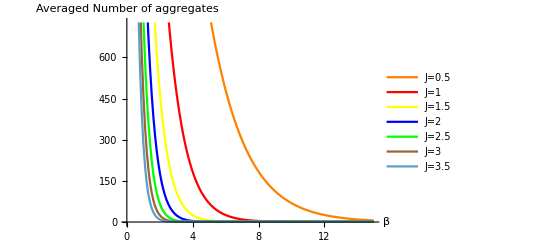

```mathematica
ListLinePlot[{(∑_(l=1)^10000 ⅇ^(-J05×l))/(∑_(l=1)^10000 l×ⅇ^(-J05×l))×10000,(∑_(l=1)^10000 ⅇ^(-J1×l))/(∑_(l=1)^10000 l×ⅇ^(-J1×l))×10000,(∑_(l=1)^10000 ⅇ^(-J105×l))/(∑_(l=1)^10000 l×ⅇ^(-J105×l))×10000,(∑_(l=1)^10000 ⅇ^(-J2×l))/(∑_(l=1)^10000 l×ⅇ^(-J2×l))×10000,(∑_(l=1)^10000 ⅇ^(-J205×l))/(∑_(l=1)^10000 l×ⅇ^(-J205×l))×10000,(∑_(l=1)^10000 ⅇ^(-J3×l))/(∑_(l=1)^10000 l×ⅇ^(-J3×l))×10000,(∑_(l=1)^10000 ⅇ^(-J305×l))/(∑_(l=1)^10000 l×ⅇ^(-J305×l))×10000},DataRange->{0,15},PlotStyle->{Orange,Red,Yellow,Blue,Green,Brown,Grey},PlotLegends->{"J=0.5","J=1","J=1.5","J=2","J=2.5","J=3","J=3.5"},AxesLabel->{"β","Total Number of aggregates"}]
```

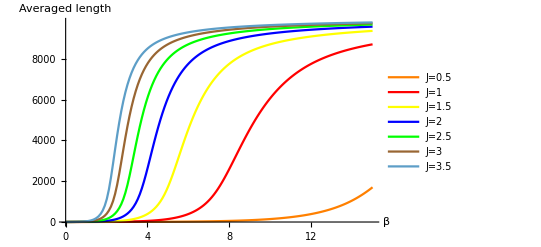

```mathematica
ListLinePlot[{(∑_(l=1)^10000 l×ⅇ^(-J05×l))/(∑_(l=1)^10000 ⅇ^(-J05×l)),(∑_(l=1)^10000 l×ⅇ^(-J1×l))/(∑_(l=1)^10000 ⅇ^(-J1×l)),(∑_(l=1)^10000 l×ⅇ^(-J105×l))/(∑_(l=1)^10000 ⅇ^(-J105×l)),(∑_(l=1)^10000 l×ⅇ^(-J2×l))/(∑_(l=1)^10000 ⅇ^(-J2×l)),(∑_(l=1)^10000 l×ⅇ^(-J205×l))/(∑_(l=1)^10000 ⅇ^(-J205×l)),(∑_(l=1)^10000 l×ⅇ^(-J3×l))/(∑_(l=1)^10000 ⅇ^(-J3×l)),(∑_(l=1)^10000 l×ⅇ^(-J305×l))/(∑_(l=1)^10000 ⅇ^(-J305×l))},DataRange->{0,15},PlotStyle->{Orange,Red,Yellow,Blue,Green,Brown,Grey},PlotLegends->{"J=0.5","J=1","J=1.5","J=2","J=2.5","J=3","J=3.5"},AxesLabel->{"β","Averaged length"}]
```